A gate is universal if all other gates are able to be made from it. For example, NAND can represent any other gate;

```mathematica
NAND[a_, b_]:=!And[a, b];
b2i[b_]:=If[b, 1, 0];
b2i[b_List]:=b2i/@b

b2v[b_Boole]:=If[b, {0, 1}, {1, 0}]
b2v[b_Integer]:=If[b==1, {0, 1}, {1, 0}]
v2b[{v1_, v2_}]:=If[{v1,v2}=={0, 1}, 1, 0]

tensor[v__]:=Flatten[TensorProduct[v]]
tensor[{0, 1}, {1, 0}, {0, 1}]
KroneckerProduct[Array[Subscript[a, ##]&, {2, 2}], Array[Subscript[b, ##]&, {2, 2}]]//MatrixForm

I2={{1, 0}, {0, 1}}
```

{0,0,0,0,0,1,0,0}

(a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,2) b_(1,1) | a_(1,2) b_(1,2)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,2) b_(2,1) | a_(1,2) b_(2,2)
a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,2) b_(1,1) | a_(2,2) b_(1,2)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,2) b_(2,1) | a_(2,2) b_(2,2))

{{1,0},{0,1}}

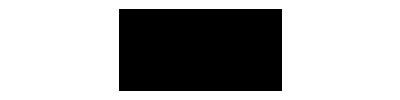

-Graphics-

```mathematica
XOR[a_, b_]:=NAND[NAND[NAND[NAND[a, a], NAND[b, b]], NAND[a, b]], NAND[NAND[NAND[a, a], NAND[b, b]], NAND[a, b]]];
ArrayPlot[{BooleanTable[b2i@Xor[p, q], {p, q}]}]
ArrayPlot[{BooleanTable[b2i@XOR[p, q], {p, q}]}]
(* 00 -> 0, 01 -> 1, 10 -> 1, 11 -> 0. Thus, {0, 1, 1, 0} *)
```

A gate such as NAND can be replaced

Adjacent swap composition approach to bigger swaps

```mathematica
matrixSWAP={{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}};
matrixNOT={{0, 1}, {1, 0}};
```

```mathematica
Vi1[i_, n_, s1_, s2_]:=Module[{bv, sbv},
bv=IntegerDigits[i, 2, n];
sbv=tensor@@(b2v/@Table[bv[[Switch[j, s1, s2, s2, s1, _, j]]], {j,n}])]
matrixSwap[n_, s1_, s2_]:=Vi1[#, n, s1, s2]&/@Range[0, 2^n-1]
```

```mathematica
matrixSwap[1, 3, 3]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
matrixCopy={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}};
matrixNand={{}}
```

{{}}

```mathematica
n=5;
gates={
{2, 3}->matrixCopy,
{2, 3}->matrixNand,
{1, 2}->matrixSwap,
{3, 4}->matrixSwap,
{2, 3}->
{2, 3}->matrixNand,
{1, 2}->matrixNand,
{3, 4}->matrixNand,
{2, 3}->matrixSwap,
{3, 4}->matrixNand,
{4, 5}->matrixCopy,
{4, 5}->matrixNand,
{5, 5}->matrixReturn
};
```

```mathematica
{0, 0, 0, 1, 1}[[4;;5]]
b2v/@%
```

{1,1}

{{0,1},{0,1}}

```mathematica
Vi2[i_, n_, s_List]:=tensor@@b2v/@(IntegerDigits[i, 2, n])[[Span@@s]]

matrixReturn[n_, s1_, s2_]:=Transpose[Vi2[#, n, {s1, s2}]&/@Range[0, 2^n-1]]
```

```mathematica
M=matrixReturn[3, {1, 1}]
%//MatrixForm
```

{{1,1,1,1,0,0,0,0},{0,0,0,0,1,1,1,1}}

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
b2v/@{0, 1, 1}
v=(tensor@@(b2v/@{0, 1, 1}));
v//MatrixForm
M.v//MatrixForm
```

{{1,0},{0,1},{0,1}}

(0
0
0
1
0
0
0
0)

(1
0)

```mathematica
matrixNand={{0, 0, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}
% // MatrixForm
```

{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}

(0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
matrixSwap[5, 1, 2]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
n=5;
gates={
{{2, 3},matrixCopy},
{{2, 3},matrixNand},
{{1, 2},matrixSwap},
{{3, 4},matrixSwap},
{{2, 3}, matrixCopy},
{{2, 3},matrixNand},
{{1, 2},matrixNand},
{{3, 4},matrixNand},
{{2, 3},matrixSwap},
{{3, 4},matrixNand},
{{4, 5},matrixCopy},
{{4, 5},matrixNand},
{{5, 5},matrixReturn}
};



(* For[i=1,i<=Length[gates],i++,Module[ *)
matrixFormOfColumn[i_Integer]:=
Module[{G, s1, s2, M},
G=gates[[i]];
s1=G[[1, 1]];
s2=G[[1,2]];
M=G[[2]];

(* Switch for irregular functions *)
OM=Switch[M,
matrixSwap,matrixSwap[n,s1,s2],
matrixReturn, matrixReturn[n, s1, s2],
_, Module[{N1, N2, N3, IN1, IN2, IN3},
N1=s1-1;
N2=s2-s1+1;
N3=n-s2;
IN1=ConstantArray[I2, N1];
IN2={M};
IN3=ConstantArray[I2, N3];
KroneckerProduct@@Join[IN1, IN2, IN3]
]
]
]
```

```mathematica
xorFromNandMatrix[a_,b_]:=Module[{currentStateVector},
currentStateVector=tensor@@b2v/@{a, b, 0, 0, 0};
For[i=1,i<=Length[gates],i++,
currentStateVector=matrixFormOfColumn[i].currentStateVector;
];
currentStateVector
]

v2b/@
{xorFromNandMatrix[0, 0],
xorFromNandMatrix[0, 1],
xorFromNandMatrix[1, 0],
xorFromNandMatrix[1, 1]}
```

{0,1,1,0}